NB: Sending χ→-χ to flip plot the right way round

ω_s<<ω_FSR?: ω_s=37500., ω_FSR=7500

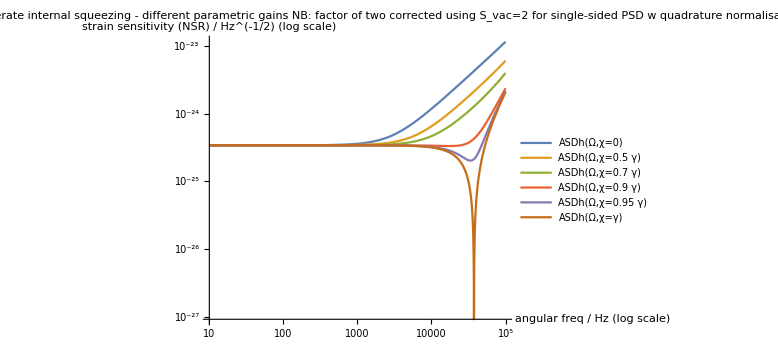

```mathematica
c=3 10^8(*ms^-1*);
ℏ=1 10^-34(*Js*);
(*Using the same values as Fig.3 in Korobko et al, 2019: benchmark 3rd generation detector*)
λ=1550 10^-9(*m*);
w0=2π c/λ;
P = 4 10^6(*W*);
Larm=20 10^3(*m*);
Lse=56(*m*);
Titm=0.07;
Tse=0.35;
ws=c(Titm/(4 Lse Larm))^(1/2);
Print[StringForm["ω_s<<ω_FSR?: ω_s=``, ω_FSR=``",ws,c/(2 Larm)]]
γ=(c Tse)/(4 Lse); (*later called kout*) (*Subscript[γ, R]=-1/(2 τRoundTripSE)Log[1-Tse]≃Tse/(2 τRoundTripSE)=(c Tse)/(4 Lse), all good!*)
(*the authors don't say what value they use for χ, threshold?*)
Sh[Ω_,χ_]:=(ℏ c)/(8 P Larm w0)(Ω^2(γ-χ)^2+(ws^2-Ω^2)^2)/(ws^2 γ)
ASDh[Ω_,χ_]:=Abs[Sh[Ω,χ]]^(1/2)
LogLogPlot[{ASDh[Ω,χ=0],ASDh[Ω,χ=0.5γ],ASDh[Ω,χ=0.7γ],ASDh[Ω,χ=0.9γ],ASDh[Ω,χ=0.95γ],ASDh[Ω,χ=γ]},{Ω,10,10^5},AxesLabel->{"angular freq / Hz (log scale)", "strain sensitivity (NSR) / Hz^(-1/2) (log scale)"},ImageSize->Large,PlotRange->All,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless degenerate internal squeezing - different parametric gains\nNB: factor of two corrected using S_vac=2 for single-sided PSD w quadrature normalisation"]
```

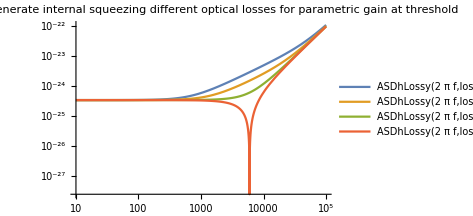
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR)
/ Hz^(-1/2) (log scale)

```mathematica
(*Lossy result*)
χ=γ;(*at threshold*)
kout=γ;
(*lossRatio=kloss/(kloss+kout),(kout*loss)/(1-loss)=kloss*)
(*have omitted factor 1/2 since it should have cancelled with quadrature normalisation in Subscript[S, vac]*)
ShLossy[Ω_,lossRatio_]:=(ℏ c)/(8 P Larm w0)(Ω^2((kout+(kout*lossRatio)/(1-lossRatio)+χ)^2-4kout χ)+(ws^2-Ω^2)^2)/(ws^2 kout)
ASDhLossy[Ω_,lossRatio_]:=Abs[ShLossy[Ω,lossRatio]]^(1/2)
Labeled[LogLogPlot[{
ASDhLossy[2π f,lossRatio=0.1],
ASDhLossy[2π f,lossRatio=0.03],
ASDhLossy[2π f,lossRatio=0.005],
ASDhLossy[2π f,lossRatio=0]},{f,10,10^5},ImageSize->350,PlotRange->All,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossy degenerate internal squeezing\ndifferent optical losses\nfor parametric gain at threshold"],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
Clear[χ]
```

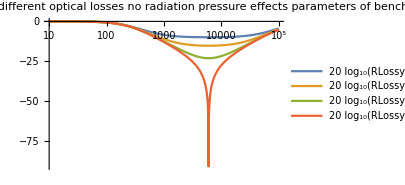
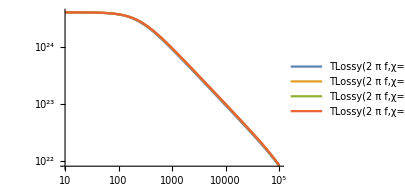
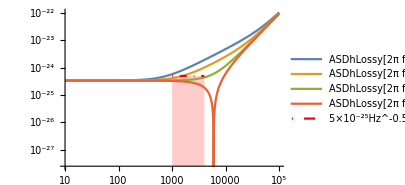
-Graphics-shot noise transfer function,
|R| / dB (20log10)
-Graphics-signal transfer function,
|T| / [?] (log scale)
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR)
/ Hz^-0.5 (log scale)

```mathematica
(*plotting |T| and (|R1|^2+|R2|^2)^(1/2)*)
Clear[χ]
G=((2P Larm w0)/(ℏ c))^(1/2);
TLossy[Ω_,χ_,lossRatio_]:=Abs[(2I ws G (2 kout)^(1/2))/(Ω(kout+(kout*lossRatio)/(1-lossRatio)+χ)+I(ws^2-Ω^2))]
(*Already calculated |R1|^2+|R2|^2 manually, see Subscript[S, Subscript[X, 1],out](Ω)*)
RLossy[Ω_,χ_,lossRatio_]:=(1-(4 Ω^2 kout χ)/(Ω^2(kout+(kout*lossRatio)/(1-lossRatio)+χ)^2+(ws^2-Ω^2)^2))^(1/2)
p1=Labeled[LogLinearPlot[{
20Log10[RLossy[2π f,χ=kout,lossRatio=0.1]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0.03]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0.005]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0]]},{f,10,10^5},ImageSize->300,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossy degenerate internal squeezing\ndifferent optical losses\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector",
ImagePadding->{{45,10},{0,0}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^5},All}],"shot noise transfer function,\n|R| / dB (20log10)",Left,RotateLabel->True,LabelStyle->Directive[10]];
p2=Labeled[LogLogPlot[{
TLossy[2π f,χ=kout,lossRatio=0.1],
TLossy[2π f,χ=kout,lossRatio=0.03],
TLossy[2π f,χ=kout,lossRatio=0.005],
TLossy[2π f,χ=kout,lossRatio=0]},{f,10,10^5},ImageSize->300,PlotRange->{{10,10^5},All},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],
ImagePadding->{{45,10},{0,5}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],}],"signal transfer function,\n|T| / [?] (log scale)",Left,RotateLabel->True,LabelStyle->Directive[10]];
χ=kout;
p3=Labeled[LogLogPlot[{
ASDhLossy[2π f,lossRatio=0.1],
ASDhLossy[2π f,lossRatio=0.03],
ASDhLossy[2π f,lossRatio=0.005],
ASDhLossy[2π f,lossRatio=0],
If[10^3<#<4 10^3,5 10^-25,Null]&[f]},{f,10,10^5},ImageSize->300,PlotRange->{{10,10^5},All},PlotLegends->LineLegend[{"ASDhLossy[2π f,lossRatio=0.1]","ASDhLossy[2π f,lossRatio=0.03]","ASDhLossy[2π f,lossRatio=0.005]","ASDhLossy[2π f,lossRatio=0]","5×10^-25Hz^-0.5 target for 1–4 kHz"},LabelStyle->Directive[10]],
ImagePadding->{{45,10},{10,5}},Filling->{5->Bottom},PlotStyle->{,,,,Directive[DotDashed,Red]}],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]];
Column[{p1,p2,p3},Spacings->0]
```

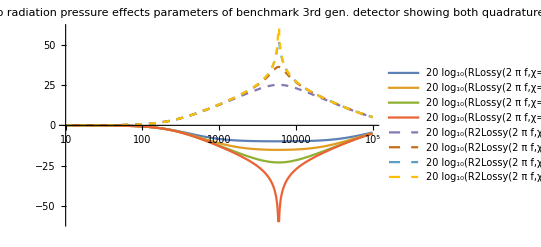
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR)
/ Hz^-0.5 (log scale)

```mathematica
(*checking other quadrature, noise transfer function is the same as before, just with χ->-χ*)

R2Lossy[Ω_,χ_,lossRatio_]:=(1+(4 Ω^2 kout χ)/(Ω^2(kout+(kout*lossRatio)/(1-lossRatio)-χ)^2+(ws^2-Ω^2)^2))^(1/2)
Labeled[LogLinearPlot[{
20Log10[RLossy[2π f,χ=kout,lossRatio=0.1]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0.03]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0.005]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0]],
20Log10[R2Lossy[2π f,χ=kout,lossRatio=0.1]],
20Log10[R2Lossy[2π f,χ=kout,lossRatio=0.03]],
20Log10[R2Lossy[2π f,χ=kout,lossRatio=0.005]],
20Log10[R2Lossy[2π f,χ=kout,lossRatio=0]]},{f,10,10^5},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossy degenerate internal squeezing\ndifferent optical losses\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector\nshowing both quadratures\nsee that optical loss affects the squeezed quadrature more,\njust like a degenerate OPO",PlotStyle->{,,,,Dashed,Dashed,Dashed,Dashed},PlotRange->{{10,10^5},{-60,60}}],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
```

```mathematica
(*to-do: plotting the same as above, but for the LIGO Voyager parameters used by Li et al, 2020 for direct comparison to those plots + conventional detector*)
```

```mathematica
(*stability of degenerate internal squeezing*)
Clear[χ,lossRatio]
ktot[lossRatio_]:=kout+(kout*lossRatio)/(1-lossRatio);
poles[χ_,lossRatio_]:={(-I (ktot[lossRatio]+χ)+(-(ktot[lossRatio]+χ)^2+4 ws^2)^(1/2))/2,(-I (ktot[lossRatio]+χ)-(-(ktot[lossRatio]+χ)^2+4 ws^2)^(1/2))/2};
Manipulate[ListPlot[{
{Re[poles[χ,lossRatio][[1]]],Im[poles[χ,lossRatio][[1]]]},
{Re[poles[χ,lossRatio][[2]]],Im[poles[χ,lossRatio][[2]]]}},PlotRange->{-10^6,10^5},AspectRatio->1,ImageSize->Small,PlotStyle->PointSize[Medium],PlotLabel->StringForm["poles of lossy transfer function\nχ/kout=``, lossRatio=``",χ/kout,lossRatio]],{{χ,0},0,2kout},{{lossRatio,0},0,1}]
Manipulate[ListPlot[{
{Re[poles[χ,lossRatio][[1]]],Im[poles[χ,lossRatio][[1]]]},
{Re[poles[χ,lossRatio][[2]]],Im[poles[χ,lossRatio][[2]]]}},PlotRange->{-10^4,10^4},AspectRatio->1,ImageSize->Small,PlotStyle->PointSize[Medium],PlotLabel->StringForm["poles of lossy transfer function\nχ/kout=``, lossRatio=``",χ/kout,lossRatio]],{{χ,0},0,2kout},{{lossRatio,0},0,1}]
```

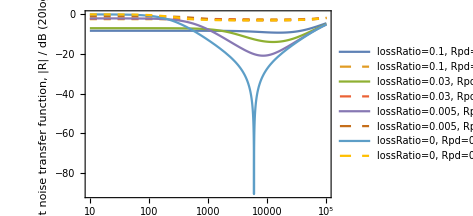
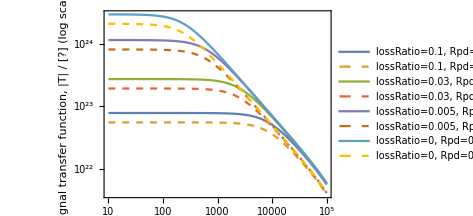
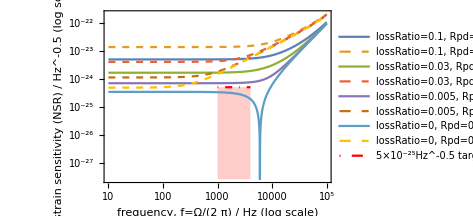

{1.78725×10^-38,{f→5968.31}}

```mathematica
(*introducing intracavity loss in â mode (κa as opposed to κaqtot, κaqout) + photodetector (PD) loss, Subscript[R, PD] is the reflectivity of the lossless beam-splitter before the PD,
copying code from above*)
Clear[χ]
κa[lossRatio_]:=(kout*lossRatio)/(1-lossRatio);
κaq[lossRatio_]:=kout+(kout*lossRatio)/(1-lossRatio);
κaqout=kout;
TPDLossy[Ω_,χ_,lossRatio_,Rpd_]:=(1-Rpd)^(1/2)Abs[(2 (κaqout)^(1/2)ws G)/((κaq[lossRatio]+χ-I Ω)(κa[lossRatio]-I Ω)+ws^2)]
RPDLossy[Ω_,χ_,lossRatio_,Rpd_]:=((1-Rpd)(
Abs[(2κaqout-κaq[lossRatio]-χ+I Ω-ws^2/(κa[lossRatio]-I Ω))/(κaq[lossRatio]+χ-I Ω+ws^2/(κa[lossRatio]-I Ω))]^2
+Abs[(2(κaqout (κaq[lossRatio]-κaqout))^(1/2))/(κaq[lossRatio]+χ-I Ω+ws^2/(κa[lossRatio]-I Ω))]^2
+Abs[(2(κaqout κa[lossRatio])^(1/2)ws)/((κaq[lossRatio]+χ-I Ω)(κa[lossRatio]-I Ω)+ws^2)]^2)+Rpd)^(1/2)
ASDhPDLossy[Ω_,χ_,lossRatio_,Rpd_]:=(1/(4 κaqout ws^2 G^2)(
((2κaqout-κaq[lossRatio]-χ)κa[lossRatio]+Ω^2-ws^2)^2
+Ω^2(κa[lossRatio]-(2κaqout-κaq[lossRatio]-χ))^2
+(κa[lossRatio]^2+ Ω^2)4κaqout (κaq[lossRatio]-κaqout)
+4κaqout κa[lossRatio] ws^2
+ Rpd/(1-Rpd)(((-κaq[lossRatio]-χ)κa[lossRatio]+Ω^2-ws^2)^2
		+Ω^2(κa[lossRatio]-(-κaq[lossRatio]-χ))^2)))^(1/2)
(*RPDLossy[Ω,χ,lossRatio,Rpd]/TPDLossy[Ω,χ,lossRatio,Rpd]*)
p1=LogLinearPlot[{
20Log10[RPDLossy[2π f,χ=kout,lossRatio=0.1,Rpd=0]],
20Log10[RPDLossy[2π f,χ=kout,lossRatio=0.1,Rpd=0.5]],
20Log10[RPDLossy[2π f,χ=kout,lossRatio=0.03,Rpd=0]],
20Log10[RPDLossy[2π f,χ=kout,lossRatio=0.03,Rpd=0.5]],
20Log10[RPDLossy[2π f,χ=kout,lossRatio=0.005,Rpd=0]],
20Log10[RPDLossy[2π f,χ=kout,lossRatio=0.005,Rpd=0.5]],
20Log10[RPDLossy[2π f,χ=kout,lossRatio=0,Rpd=0]],
20Log10[RPDLossy[2π f,χ=kout,lossRatio=0,Rpd=0.5]]},{f,10,10^5},ImageSize->350,PlotLegends->LineLegend[{"lossRatio=0.1, Rpd=0","lossRatio=0.1, Rpd=0.5","lossRatio=0.03, Rpd=0","lossRatio=0.03, Rpd=0.5","lossRatio=0.005, Rpd=0","lossRatio=0.005, Rpd=0.5","lossRatio=0, Rpd=0","lossRatio=0, Rpd=0.5"},LabelStyle->Directive[10]],
ImagePadding->{{90,10},{1,100}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^5},All},PlotStyle->{,Dashed},Frame->True,FrameLabel->{{"shot noise transfer function,\n|R| / dB (20log10)",},{,"lossy degenerate internal squeezing\ndifferent optical losses\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector at threshold\nwith â mode intracavity loss and PD loss"}}];
p2=LogLogPlot[{
TPDLossy[2π f,χ=kout,lossRatio=0.1,Rpd=0],
TPDLossy[2π f,χ=kout,lossRatio=0.1,Rpd=0.5],
TPDLossy[2π f,χ=kout,lossRatio=0.03,Rpd=0],
TPDLossy[2π f,χ=kout,lossRatio=0.03,Rpd=0.5],
TPDLossy[2π f,χ=kout,lossRatio=0.005,Rpd=0],
TPDLossy[2π f,χ=kout,lossRatio=0.005,Rpd=0.5],
TPDLossy[2π f,χ=kout,lossRatio=0,Rpd=0],
TPDLossy[2π f,χ=kout,lossRatio=0,Rpd=0.5]},{f,10,10^5},ImageSize->350,PlotRange->{{10,10^5},All},PlotLegends->LineLegend[{"lossRatio=0.1, Rpd=0","lossRatio=0.1, Rpd=0.5","lossRatio=0.03, Rpd=0","lossRatio=0.03, Rpd=0.5","lossRatio=0.005, Rpd=0","lossRatio=0.005, Rpd=0.5","lossRatio=0, Rpd=0","lossRatio=0, Rpd=0.5"},LabelStyle->Directive[10]],
ImagePadding->{{90,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotStyle->{,Dashed},Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}}];
p3=LogLogPlot[{
ASDhPDLossy[2π f,χ=kout,lossRatio=0.1,Rpd=0],
ASDhPDLossy[2π f,χ=kout,lossRatio=0.1,Rpd=0.5],
ASDhPDLossy[2π f,χ=kout,lossRatio=0.03,Rpd=0],
ASDhPDLossy[2π f,χ=kout,lossRatio=0.03,Rpd=0.5],
ASDhPDLossy[2π f,χ=kout,lossRatio=0.005,Rpd=0],
ASDhPDLossy[2π f,χ=kout,lossRatio=0.005,Rpd=0.5],
ASDhPDLossy[2π f,χ=kout,lossRatio=0,Rpd=0],
ASDhPDLossy[2π f,χ=kout,lossRatio=0,Rpd=0.5],
If[10^3<#<4 10^3,5 10^-25,Null]&[f]},{f,10,10^5},ImageSize->350,PlotRange->{{10,10^5},All},PlotLegends->LineLegend[{"lossRatio=0.1, Rpd=0","lossRatio=0.1, Rpd=0.5","lossRatio=0.03, Rpd=0","lossRatio=0.03, Rpd=0.5","lossRatio=0.005, Rpd=0","lossRatio=0.005, Rpd=0.5","lossRatio=0, Rpd=0","lossRatio=0, Rpd=0.5","5×10^-25Hz^-0.5 target for 1–4 kHz"},LabelStyle->Directive[10]],
ImagePadding->{{90,10},{50,1}},Filling->{9->Bottom},PlotStyle->{,Dashed,,Dashed,,Dashed,,Dashed,Directive[DotDashed,Red]},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",}}];
Column[{p1,p2,p3},Spacings->0]
(*to-do: fix Legend labels to be "Expressions"+(joined to)+"5×10^-25Hz^-0.5 target for 1–4 kHz"
NB: this is fiddly and there are problems with slicing existing labels
---> this has been fixed using the custom function labeller[...] below for external squeezing
to-do: fix legend alignment and size
https://mathematica.stackexchange.com/questions/204519/barlegend-framelabel-ruins-alignment-of-barlegend*)
Minimize[{ASDhPDLossy[2π f,χ=kout,lossRatio=0,Rpd=0],f>0},f]
```

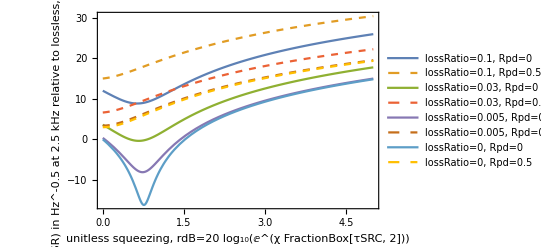

rdB→0.760015

To a tolerance of 0.00001, the optimum χ is on threshold: True

```mathematica
(*sensitivity at 2.5 kHz versus squeezer parameter, want to illustrate threshold of χ=kout
plot dB on yaxis against value at threshold or at no squeezing?
plot dB on xaxis for rdB=20 Log10[Exp[χ τSRC/2]],χ=2/τSRC Log[10^(rdB/20)]*)
fProbe=2.5 10^3(*Hz, ws/(2π) more resembles above*);
sensRef = ASDhPDLossy[2π fProbe,0,lossRatio=0,Rpd=0];(*sensitivity reference: lossless, no squeezing, i.e. conventional*)
τSE=(2 Lse)/c; (*round-trip*)
Plot[{
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0.1,Rpd=0]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0.1,Rpd=0.5]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0.03,Rpd=0]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0.03,Rpd=0.5]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0.005,Rpd=0]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0.005,Rpd=0.5]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0,Rpd=0]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0,Rpd=0.5]/sensRef]},{rdB,0,5},PlotRange->All,PlotLegends->LineLegend[{"lossRatio=0.1, Rpd=0","lossRatio=0.1, Rpd=0.5","lossRatio=0.03, Rpd=0","lossRatio=0.03, Rpd=0.5","lossRatio=0.005, Rpd=0","lossRatio=0.005, Rpd=0.5","lossRatio=0, Rpd=0","lossRatio=0, Rpd=0.5"},LabelStyle->Directive[10]],PlotStyle->{,Dashed,,Dashed,,Dashed,,Dashed},Frame->True,FrameLabel->{{StringForm["strain sensitivity (NSR) in Hz^-0.5 at `` kHz\nrelative to lossless, no squeezing value / dB",fProbe/10^3],},{"unitless squeezing, rdB=20 log_10(ⅇ^(χ FractionBox[τSRC, 2]))","lossy degenerate internal squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector\nwith â mode intracavity loss and PD loss"}}]
(*showing that minimum is indeed χ=kout*)
thresholdrdB = Minimize[{20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0,Rpd=0]/sensRef],rdB>0},{rdB}][[2]][[1]]
thresholdχ=2/τSE Log[10^(rdB/20)]/.thresholdrdB;
tolerance=N[10^-5];
Print[StringForm["To a tolerance of ``, the optimum χ is on threshold: ",tolerance],Abs[(thresholdχ-kout)/kout]<tolerance]
```

```mathematica
(*want to model external squeezing, first: check that degenerate internal squeezing returns conventional detector when χ=0
have to clear kernel first*)
(*Clear[χ,lossRatio,Rpd]
ASDhPDLossy[Ω,χ=0,lossRatio,Rpd]^2/.{χ->0,κa->(0&),κaqout->κaq[lossRatio],Rpd->0}/.{κaq[lossRatio]->κaq}*)
```

```mathematica
(*external squeezing injected into conventional detector*)
(*pulling values from Wade et al, 2016 - https://aip.scitation.org/doi/pdf/10.1063/1.4953326*)
Clear[Rpd]
TExt=0.155;
LExt=0.18;(*m*)
τRoundTripExt=(2 LExt)/c;
κafExt=-1/(2 τRoundTripExt)Log[1-TExt];(*aka. κaoutExt*)
(*now quoting losses as Subscript[T, l], transmitivity (of power/energy) of loss port mirror, instead of using loss ratio=1-ηesc*)
κaExt[TlExt_]:=κafExt+-1/(2 τRoundTripExt)Log[1-TlExt]
VExt[Ω_,gExt_,Rinj_,TlExt_]:=1-(4 κafExt gExt)/((κaExt[TlExt]+gExt)^2+Ω^2)(1-Rinj)
τRoundTripArm=(2 Larm)/c;
τRoundTripSE=(2 Lse)/c;
κa[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla];
κaqout=kout;
κaq[Tlaq_]:=κaqout+-1/(2 τRoundTripSE)Log[1-Tlaq];
RIntExtSqz[Ω_,χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_]:=((1-Rpd)(
VExt[Ω,gExt,Rinj,TlExt] Abs[(2κaqout-κaq[Tlaq]-χ+I Ω-ws^2/(κa[Tla]-I Ω))/(κaq[Tlaq]+χ-I Ω+ws^2/(κa[Tla]-I Ω))]^2
+Abs[(2(κaqout (κaq[Tlaq]-κaqout))^(1/2))/(κaq[Tlaq]+χ-I Ω+ws^2/(κa[Tla]-I Ω))]^2
+Abs[(2(κaqout κa[Tla])^(1/2)ws)/((κaq[Tlaq]+χ-I Ω)(κa[Tla]-I Ω)+ws^2)]^2)+Rpd)^(1/2)
TIntExtSqz[Ω_,χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_]:=(1-Rpd)^(1/2)Abs[(2 (κaqout)^(1/2)ws G)/((κaq[Tlaq]+χ-I Ω)(κa[Tla]-I Ω)+ws^2)]
ASDShIntExtSqz[Ω_,χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_]:=(1/(4 κaqout ws^2 G^2)(
VExt[Ω,gExt,Rinj,TlExt](((2κaqout-κaq[Tlaq]-χ)κa[Tla]+Ω^2-ws^2)^2
						+Ω^2(κa[Tla]-(2κaqout-κaq[Tlaq]-χ))^2)
+(κa[Tla]^2+ Ω^2)4κaqout (κaq[Tlaq]-κaqout)
+4κaqout κa[Tla] ws^2
+ Rpd/(1-Rpd)(((-κaq[Tlaq]-χ)κa[Tla]+Ω^2-ws^2)^2
		+Ω^2(κa[Tla]-(-κaq[Tlaq]-χ))^2)))^(1/2)
```

```mathematica
(*automated plotting, just enter values into valsList*)
unpackRIntExtSqz[Ω_,vals_]:=RIntExtSqz[Ω,vals[[1]],vals[[2]],vals[[3]],vals[[4]],vals[[5]],vals[[6]],vals[[7]]]
unpackTIntExtSqz[Ω_,vals_]:=TIntExtSqz[Ω,vals[[1]],vals[[2]],vals[[3]],vals[[4]],vals[[5]],vals[[6]],vals[[7]]]
unpackASDShIntExtSqz[Ω_,vals_]:=ASDShIntExtSqz[Ω,vals[[1]],vals[[2]],vals[[3]],vals[[4]],vals[[5]],vals[[6]],vals[[7]]]
(*each vals contains: {χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_}*)
labeller[vals_]:=(
paddedStrings=StringPadRight[{
ToString[N[vals[[1]]/κaqout]],
ToString[N[vals[[2]]/κafExt]],
ToString[vals[[3]]],
ToString[vals[[4]]],
ToString[vals[[5]]],
ToString[vals[[6]]],
ToString[vals[[7]]]},4];
Style[If[vals[[2]]==0,
StringForm["χ/κ_a_q=``; T_(l, a)=``, T_(l, SubscriptBox[a, q])=``, R_PD=``",
paddedStrings[[1]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]]],
StringForm["χ/κ_a_q=`1`; T_(l, a)=`3`, T_(l, SubscriptBox[a, q])=`4`, R_PD=`5`; g_ext/κ_(af, ext)=`2`, T_(l, ext)=`7`, R_inj=`6`",
paddedStrings[[1]],
paddedStrings[[2]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]],
paddedStrings[[6]],
paddedStrings[[7]]]],FontFamily->"Monospace"])

plotIntExtSqz[valsList_,plotLabel_:"internal/external squeezing",plotStyle_:{},legendLabel_:None]:=(
p1=LogLinearPlot[Evaluate[Table[20Log10[unpackRIntExtSqz[2π f,valsList[[i]]]],{i,1,Length[valsList]}]],
{f,10,10^5},ImageSize->350,Frame->True,PlotLegends->LineLegend[Table[labeller[valsList[[i]]],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}},LegendLabel->legendLabel],
ImagePadding->{{100,10},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^5},All},PlotStyle->plotStyle,FrameLabel->{{"shot noise transfer function,\n|R| / dB (20log10)",},{,plotLabel}}];
p2=LogLogPlot[Evaluate[Table[unpackTIntExtSqz[2π f,valsList[[i]]],{i,1,Length[valsList]}]],
{f,10,10^5},ImageSize->350,PlotRange->{{10,10^5},All},PlotLegends->LineLegend[Table[labeller[valsList[[i]]],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],
ImagePadding->{{100,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}}];
p3=LogLogPlot[Evaluate[Join[Table[unpackASDShIntExtSqz[2π f,valsList[[i]]],{i,1,Length[valsList]}],{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],{f,10,10^5},ImageSize->350,PlotRange->{{10,10^5},All},PlotLegends->LineLegend[Join[Table[labeller[valsList[[i]]],{i,1,Length[valsList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],
ImagePadding->{{100,10},{50,1}},Filling->{Length[valsList]+1->Bottom},PlotStyle->If[plotStyle=={},Join[Table[,{n,1,Length[valsList]}],{Directive[DotDashed,Red]}],Join[plotStyle,{Directive[DotDashed,Red]}]],Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",}}];
Column[{p1,p2,p3},Spacings->0])
```

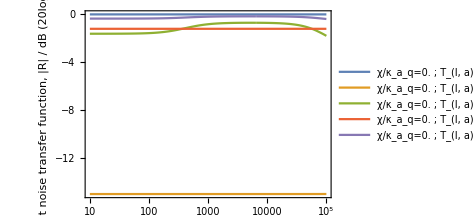
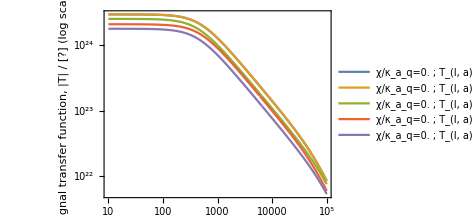
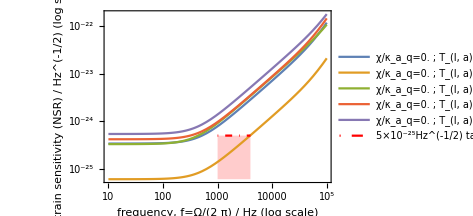

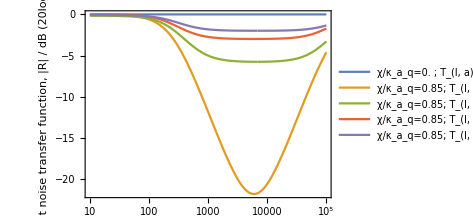
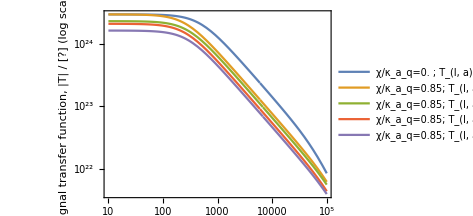
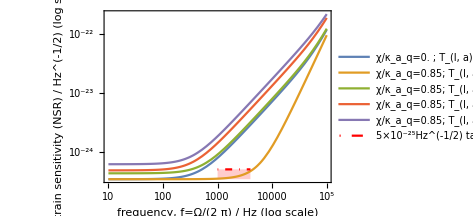

```mathematica
(*specify dB of injected squeezing*)
injdB=15(*dB*);
Clear[r]
gExtRatio0=(r/.Minimize[Abs[20Log10[unpackRIntExtSqz[1,{0kout,r κafExt,0,0,0,0,0}]]-(-injdB)],r][[2,1]]);
(*each vals contains: {χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_}*)
valsList0={
{0kout,0κafExt,0,0,0,0,0},
{0kout,gExtRatio0 κafExt,0,0,0,0,0},
{0kout,gExtRatio0 κafExt,0.1,0.1,0,0,0.1},
{0kout,gExtRatio0 κafExt,0,0,0.5,0.5,0},
{0kout,gExtRatio0 κafExt,0.1,0.1,0.5,0.5,0.1}};
plotIntExtSqz[valsList0,"lossy external squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector"]

(*input ratio of squeezing parameter to threshold*)
χRatio0=0.85;
valsList1={
{0kout,0κafExt,0,0,0,0,0},
{χRatio0 kout,0κafExt,0,0,0,0,0},
{χRatio0 kout,0κafExt,0.1,0.1,0,0,0},
{χRatio0 kout,0κafExt,0,0,0.5,0,0},
{χRatio0 kout,0κafExt,0.1,0.1,0.5,0,0}};
plotIntExtSqz[valsList1,"lossy degenerate internal squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector"]
```

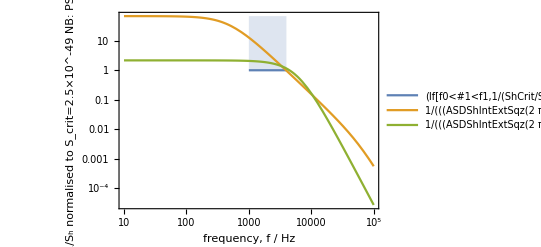

For S_h(Ω) given by: ASDShIntExtSqz[#1,0 kout,0 κafExt,0,0,0,0,0]^2&
--> μtric0=0. (unitless)

For S_h(Ω) given by: ASDShIntExtSqz[#1,0 kout,gExtRatio0 κafExt,0,0,0,0,0]^2&
--> μtric0=2.59415 (unitless)

For S_h(Ω) given by: ASDShIntExtSqz[#1,χRatio0 kout,0 κafExt,0,0,0,0,0]^2&
--> μtric0=0.648457 (unitless)

```mathematica
(*implementing a simple metric to quantify how well the target sensitivity is achieved*)
{f0, f1} = {1 10^3,4 10^3};(*Hz*)
ASDShCrit = 5 10^-25;(*Hz^(-1/2)*)
ShCrit=ASDShCrit^2;(*Hz^-1*)
LogLogPlot[{
If[f0<#<f1,1/ShCrit/(1/ShCrit),Null]&[f],
1/ASDShIntExtSqz[2π f,0kout,gExtRatio0 κafExt,0,0,0,0,0]^2/(1/ShCrit),
1/ASDShIntExtSqz[2π f,χRatio0 kout,0κafExt,0,0,0,0,0]^2/(1/ShCrit)},{f,10,10^5},Filling->{1->Top},PlotLegends->"Expressions",Frame->True,FrameLabel->{{StringForm["SNR, 1/S_h\nnormalised to S_crit=``\nNB: PSD not ASD",N[ShCrit]],},{"frequency, f / Hz", "SNR used to calculate μtric"}}]

(*in order for numerical optimisation to work, need to have μtric0 only evaluate if fed a numerical argument by using ?NumericQ*)
(*using reciprocals by precedent set by Li et al comparison of bandwidth--peak sensitivity product*)
μtric0[fnSh_]:=1/(f1-f0)NIntegrate[Max[1/fnSh[2π f]-1/ShCrit,0]/(1/ShCrit),{f,f0,f1}]
printμtric0[fnSh_]:=Print[StringForm["For S_h(Ω) given by: ``\n--> μtric0=`` (unitless)",fnSh,NumberForm[μtric0[fnSh]]]]

printμtric0[ASDShIntExtSqz[#,0kout,0κafExt,0,0,0,0,0]^2&]
printμtric0[ASDShIntExtSqz[#,0kout,gExtRatio0 κafExt,0,0,0,0,0]^2&]
printμtric0[ASDShIntExtSqz[#,χRatio0 kout,0κafExt,0,0,0,0,0]^2&]
```

```mathematica
(* commenting out optimisation for now

(*optimisation: tutorial -- https://support.wolfram.com/12502*)
reduSh0[Ω_?NumericQ,r_?NumericQ]:=ASDShIntExtSqz[Ω,0 kout,r κafExt,0,0,0,0,0]^2
(*Mathematica gets upset passing pure functions to NMaximize?*)
optiFn0[r_?NumericQ]:=μtric0[reduSh0[#,r]&]
(*NMaximize[{μtric0[reduSh[#,r]&],0.4<r<0.7},r]*)
(*because of zeroing of μtric0, optimisation must be run from a non-zero starting value -- to-do: fix this*)
optiVals0=NMaximize[{optiFn0[r],0.4<r<1},r]
printμtric0[ASDShIntExtSqz[#,0kout,(r/.optiVals0[[2]][[1]]) κafExt,0,0,0,0,0]^2&]
(*NB: gExtRatio0=0.698*)
(*given external squeezing, the optimiser finds threshold*)
-Graphics-;
(*do the same for internal squeezing*)
reduSh1[Ω_?NumericQ,r_?NumericQ]:=ASDShIntExtSqz[Ω,r kout,0 κafExt,0,0,0,0,0]^2
optiFn1[r_?NumericQ]:=μtric0[reduSh1[#,r]&]
optiVals1=NMaximize[{optiFn1[r],0.4<r<1},r]
printμtric0[ASDShIntExtSqz[#,(r/.optiVals1[[2]][[1]])kout,0 κafExt,0,0,0,0,0]^2&]
(*for internal squeezing, optimiser finds threshold again*)
-Graphics-;
(*if optimisation spits out more interesting results, then plot them using plotIntExtSqz*)

*)
```

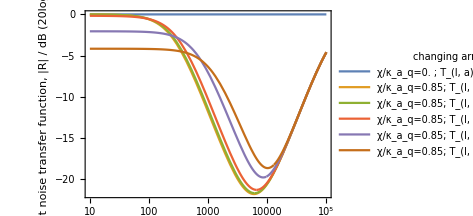
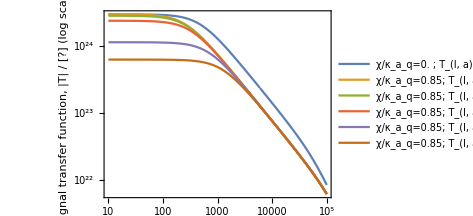
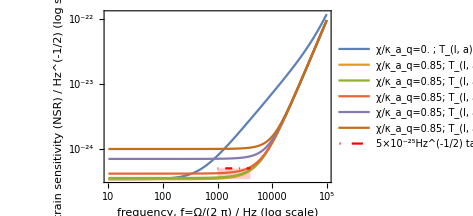

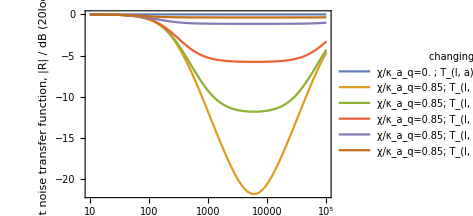
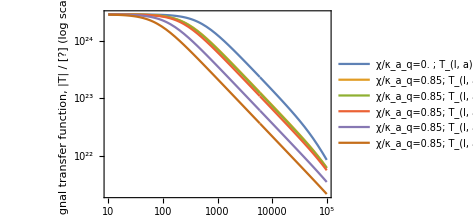
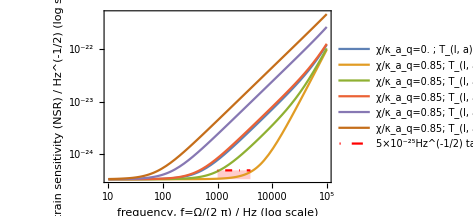

```mathematica
(*setting SRC to be lossless*)
(*each vals contains: {χ_,gExt_,Tla_,Tlaq_,Rpd_,Rinj_,TlExt_}*)
valsList1={
{0kout,0κafExt,0,0,0,0,0},
{χRatio0 kout,0κafExt,0,0,0,0,0},
{χRatio0 kout,0κafExt,0.02,0,0,0,0},
{χRatio0 kout,0κafExt,0.1,0,0,0,0},
{χRatio0 kout,0κafExt,0.5,0,0,0,0},
{χRatio0 kout,0κafExt,0.8,0,0,0,0}};
plotIntExtSqz[valsList1,"lossy degenerate internal squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector",{},"changing arm cavity intra-cavity loss"]
valsList1={
{0kout,0κafExt,0,0,0,0,0},
{χRatio0 kout,0κafExt,0,0,0,0,0},
{χRatio0 kout,0κafExt,0,0.02,0,0,0},
{χRatio0 kout,0κafExt,0,0.1,0,0,0},
{χRatio0 kout,0κafExt,0,0.5,0,0,0},
{χRatio0 kout,0κafExt,0,0.8,0,0,0}};
plotIntExtSqz[valsList1,"lossy degenerate internal squeezing\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector",{},"changing SRC intra-cavity loss"]
```